# lorentzian smearing

## g switch, L smear, go futher with the transition probability

## the smearing function

```mathematica
f[x_]:=σ/π 1/(x^2+σ^2)
ftil[k_]:=FourierTransform[f[x],x,k,FourierParameters->{1,-1}]
```

#### simplify the fourier transform

```mathematica
ftil[k]
```

1/2 ⅇ^(-k σ) ((-1+ⅇ^(2 k σ)) Sign[k] (-1+Sign[Abs[Re[σ]]])+2 (ⅇ^(2 k σ) HeavisideTheta[-k Sign[Re[σ]]]+HeavisideTheta[k Sign[Re[σ]]]) Sign[Re[σ]])

```mathematica
Simplify[%,Assumptions->σ∈Reals&&σ>0]
```

```mathematica
ⅇ^(k σ) HeavisideTheta[-k]+ⅇ^(-k σ) HeavisideTheta[k]
```

```mathematica
ftilLs[k_]:=ⅇ^(-k*σ)
```

## the transition probability

```mathematica
ggintegrandL[k_]:=-1/(2π)ⅇ^(-ε*k-1/2*η^2*(Ω+k)^2)*(-1+α*(2+ⅇ^(2*η^2*Ω*k)))*k*ftilLs[k]^2
```

### with an ε regularized cutoff (exp)

```mathematica
Integrate[ggintegrandL[k],{k,0,∞},Assumptions->σ∈Reals&&σ>0&&η∈Reals&&η>0&&ε∈Reals&&ε>0&&Ω∈Reals]
```

-(ⅇ^(-1/2 η^2 Ω^2) (ⅇ^(((ε+2 σ-η^2 Ω)^2)/(2 η^2)) √(2 π) α (ε+2 σ-η^2 Ω)^2 Abs[ε+2 σ+η^2 Ω] Erf[Abs[ε+2 σ-η^2 Ω]/(√2 η)]+Abs[ε+2 σ-η^2 Ω] ((2 (-1+3 α) η-ⅇ^(((ε+2 σ-η^2 Ω)^2)/(2 η^2)) √(2 π) α (ε+2 σ-η^2 Ω)-ⅇ^(((ε+2 σ+η^2 Ω)^2)/(2 η^2)) √(2 π) (-1+2 α) (ε+2 σ+η^2 Ω)) Abs[ε+2 σ+η^2 Ω]+ⅇ^(((ε+2 σ+η^2 Ω)^2)/(2 η^2)) √(2 π) (-1+2 α) (ε+2 σ+η^2 Ω)^2 Erf[Abs[ε+2 σ+η^2 Ω]/(√2 η)])))/(4 π η^3 Abs[ε+2 σ-η^2 Ω] Abs[ε+2 σ+η^2 Ω])

```mathematica
Simplify[%,Assumptions->σ∈Reals&&σ>0&&η∈Reals&&η>0&&ε∈Reals&&ε>0&&Ω∈Reals]
```

-(ⅇ^(-1/2 η^2 Ω^2) (ⅇ^(((ε+2 σ-η^2 Ω)^2)/(2 η^2)) √(2 π) α (ε+2 σ-η^2 Ω)^2 Abs[ε+2 σ+η^2 Ω] Erf[Abs[ε+2 σ-η^2 Ω]/(√2 η)]+Abs[ε+2 σ-η^2 Ω] ((2 (-1+3 α) η-ⅇ^(((ε+2 σ-η^2 Ω)^2)/(2 η^2)) √(2 π) α (ε+2 σ-η^2 Ω)-ⅇ^(((ε+2 σ+η^2 Ω)^2)/(2 η^2)) √(2 π) (-1+2 α) (ε+2 σ+η^2 Ω)) Abs[ε+2 σ+η^2 Ω]+ⅇ^(((ε+2 σ+η^2 Ω)^2)/(2 η^2)) √(2 π) (-1+2 α) (ε+2 σ+η^2 Ω)^2 Erf[Abs[ε+2 σ+η^2 Ω]/(√2 η)])))/(4 π η^3 Abs[ε+2 σ-η^2 Ω] Abs[ε+2 σ+η^2 Ω])

```mathematica
FullSimplify[%,Assumptions->σ∈Reals&&σ>0&&η∈Reals&&η>0&&ε∈Reals&&ε>0&&Ω∈Reals]
```

```mathematica
pertexp[σ_,η_]:=-1/(4 π η^3)ⅇ^(-1/2 η^2 Ω^2) (-2 η+6 α η-ⅇ^(((ε+2 σ-η^2 Ω)^2)/(2 η^2)) √(2 π) α (ε+2 σ-η^2 Ω)+√(2 π) (ⅇ^(((ε+2 σ-η^2 Ω)^2)/(2 η^2)) α (ε+2 σ-η^2 Ω) Erf[(ε+2 σ-η^2 Ω)/(√2 η)]-ⅇ^(((ε+2 σ+η^2 Ω)^2)/(2 η^2)) (-1+2 α) (ε+2 σ+η^2 Ω) Erfc[(ε+2 σ+η^2 Ω)/(√2 η)]))
```

```mathematica
pexp[σ_,η_]:=α+λ^2*pertexp[σ,η]
```

### with no cutoff (ε:=0)

```mathematica
Simplify[pertexp[σ,η],Assumptions->ε==0]
```

```mathematica
pertnone[σ_,η_]:=1/(4 π η^3)ⅇ^(-1/2 η^2 Ω^2) (2 η-6 α η-ⅇ^(((-2 σ+η^2 Ω)^2)/(2 η^2)) √(2 π) α (2 σ-η^2 Ω) (-1+Erf[(2 σ-η^2 Ω)/(√2 η)])+ⅇ^(((2 σ+η^2 Ω)^2)/(2 η^2)) √(2 π) (-1+2 α) (2 σ+η^2 Ω) Erfc[(2 σ+η^2 Ω)/(√2 η)])
```

```mathematica
FullSimplify[%,Assumptions->σ∈Reals&&σ>0&&η∈Reals&&η>0&&Ω∈Reals]
```

```mathematica
1/(4 π η^3)ⅇ^(-1/2 η^2 Ω^2) ((2-6 α) η+ⅇ^(((-2 σ+η^2 Ω)^2)/(2 η^2)) √(2 π) (α (2 σ-η^2 Ω) Erfc[(2 σ-η^2 Ω)/(√2 η)]+ⅇ^(4 σ Ω) (-1+2 α) (2 σ+η^2 Ω) Erfc[(2 σ+η^2 Ω)/(√2 η)]))
```

```mathematica
pnone[σ_,η_]:=α+λ^2*pertnone[σ,η]
```

### with a sharp cutoff (ε:=0 and integrate only up to a constant)

```mathematica
Integrate[ggintegrandL[k],{k,0,5*Ω},Assumptions->Ω∈Reals&&Ω>0&&η∈Reals&&η>0&&σ∈Reals&&σ>0&&ε∈Reals&&ε==0]
```

```mathematica
-1/(2 π)ⅇ^(-1/2 η^2 Ω^2) (-1/(√(η^2))√2 ⅇ^(((-2 σ-η^2 Ω)^2)/(2 η^2)) (-(1-ⅇ^(-((2 σ+η^2 Ω)^2)/(2 η^2)))/(√2 η)+(1-ⅇ^(-(2 (σ+3 η^2 Ω)^2)/η^2))/(√2 η)+(√π σ Erf[(√2 σ)/η+(η Ω)/(√2)])/η^2+1/2 √π Ω Erf[(√2 σ)/η+(η Ω)/(√2)]-(√π σ Erf[(√2 σ)/η+3 √2 η Ω])/η^2-1/2 √π Ω Erf[(√2 σ)/η+3 √2 η Ω])+1/(√(η^2))2 √2 ⅇ^(((-2 σ-η^2 Ω)^2)/(2 η^2)) α (-(1-ⅇ^(-((2 σ+η^2 Ω)^2)/(2 η^2)))/(√2 η)+(1-ⅇ^(-(2 (σ+3 η^2 Ω)^2)/η^2))/(√2 η)+(√π σ Erf[(√2 σ)/η+(η Ω)/(√2)])/η^2+1/2 √π Ω Erf[(√2 σ)/η+(η Ω)/(√2)]-(√π σ Erf[(√2 σ)/η+3 √2 η Ω])/η^2-1/2 √π Ω Erf[(√2 σ)/η+3 √2 η Ω])+1/(√(η^2))√2 ⅇ^(((-2 σ+η^2 Ω)^2)/(2 η^2)) α (-(1-ⅇ^(-((-2 σ+η^2 Ω)^2)/(2 η^2)))/(√2 η)+(1-ⅇ^(-(2 (σ+2 η^2 Ω)^2)/η^2))/(√2 η)-(√π σ Erf[(√2 σ)/η+2 √2 η Ω])/η^2+1/2 √π Ω Erf[(√2 σ)/η+2 √2 η Ω]-(√π σ (-2 σ+η^2 Ω) Erf[Abs[-2 σ+η^2 Ω]/(√2 η)])/(η^2 Abs[2 σ-η^2 Ω])+(√π Ω (-2 σ+η^2 Ω) Erf[Abs[-2 σ+η^2 Ω]/(√2 η)])/(2 Abs[2 σ-η^2 Ω])))
```

```mathematica
Simplify[%,Assumptions->σ∈Reals&&σ>0&&η∈Reals&&η>0&&ε==0&&Ω∈Reals&&Ω>0]
```

```mathematica
pertsharp[σ_,η_]:=1/(4 π η^3 Abs[2 σ-η^2 Ω])ⅇ^(-2 Ω (5 σ+9 η^2 Ω)) (2 ⅇ^(10 η^2 Ω^2) α η Abs[2 σ-η^2 Ω]+2 (-1+2 α) η Abs[2 σ-η^2 Ω]-2 ⅇ^(5/2 Ω (4 σ+7 η^2 Ω)) (-1+3 α) η Abs[2 σ-η^2 Ω]-ⅇ^((2 (σ+3 η^2 Ω)^2)/η^2) √(2 π) (-1+2 α) (2 σ+η^2 Ω) Abs[2 σ-η^2 Ω] (Erf[(2 σ+η^2 Ω)/(√2 η)]-Erf[(√2 (σ+3 η^2 Ω))/η])-ⅇ^((2 σ^2)/η^2+8 σ Ω+18 η^2 Ω^2) √(2 π) α (2 σ-η^2 Ω) (-Abs[2 σ-η^2 Ω] Erf[(√2 (σ+2 η^2 Ω))/η]+(2 σ-η^2 Ω) Erf[Abs[2 σ-η^2 Ω]/(√2 η)]))
```

```mathematica
FullSimplify[%,Assumptions->σ∈Reals&&σ>0&&η∈Reals&&η>0&&ε==0&&Ω∈Reals&&Ω>0]
```

1/(4 π η^3)ⅇ^(-2 Ω (5 σ+9 η^2 Ω)) (2 (-1+ⅇ^(5/2 Ω (4 σ+7 η^2 Ω)) (1-3 α)+2 α+ⅇ^(10 η^2 Ω^2) α) η+ⅇ^((2 σ^2)/η^2+8 σ Ω+18 η^2 Ω^2) √(2 π) (α (2 σ-η^2 Ω) (-Erf[(2 σ-η^2 Ω)/(√2 η)]+Erf[(√2 (σ+2 η^2 Ω))/η])+ⅇ^(4 σ Ω) (-1+2 α) (2 σ+η^2 Ω) (-Erf[(2 σ+η^2 Ω)/(√2 η)]+Erf[(√2 (σ+3 η^2 Ω))/η])))

```mathematica
1/(4 π η^3)ⅇ^(-2 Ω (5 σ+9 η^2 Ω)) (2 (-1+ⅇ^(5/2 Ω (4 σ+7 η^2 Ω)) (1-3 α)+2 α+ⅇ^(10 η^2 Ω^2) α) η+ⅇ^((2 σ^2)/η^2+8 σ Ω+18 η^2 Ω^2) √(2 π) (α (2 σ-η^2 Ω) (-Erf[(2 σ-η^2 Ω)/(√2 η)]+Erf[(√2 (σ+2 η^2 Ω))/η])+ⅇ^(4 σ Ω) (-1+2 α) (2 σ+η^2 Ω) (-Erf[(2 σ+η^2 Ω)/(√2 η)]+Erf[(√2 (σ+3 η^2 Ω))/η])))
```

```mathematica
psharp[σ_,η_]:=α+λ^2*pertsharp[σ,η]
```

#### with a different cutoff (later) (ε:=0 and cutoff[k_]:=something)

## plot p v σ

#### assign the parameters numbers

```mathematica
η:=1
Ω:=1
α:=1
λ:=0.1
ε:=.25
```

#### clear the parameters of their numbers when necessary

```mathematica
Clear[σ];Clear[η];Clear[Ω];Clear[α];Clear[λ];Clear[ε];
```

#### plot p v σ

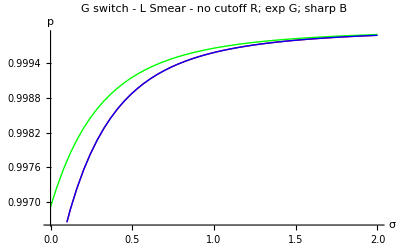

```mathematica
Plot[{pnone[σ,η],pexp[σ,η],psharp[σ,η]},{σ,0,2},
AxesLabel->{σ,p},
PlotStyle->{Red, Green, Blue},
PlotLabel->Style["G switch - L Smear - no cutoff R; exp G; sharp B",FontSize->16],
PerformanceGoal->"Quality"]
```

## plot p v σ for several values of η

#### parameterrrrrrs

```mathematica
Ω:=1
α:=1
λ:=0.1
ε:=0.25
η:={0.1,0.5,1.0,1.5}
```

#### cleeeaaaaar

```mathematica
Clear[σ];Clear[η];Clear[Ω];Clear[α];Clear[λ];Clear[ε];
```

#### plooooooooot PNONE

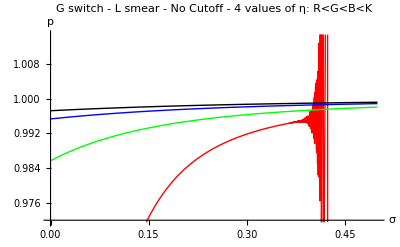

```mathematica
Plot[{pnone[σ,η[[1]]],pnone[σ,η[[2]]],pnone[σ,η[[3]]],pnone[σ,η[[4]]]},
{σ,0,.5},
AxesLabel->{σ,p},
PlotStyle->{Red,Green,Blue,Black},
PlotRange->Automatic,
PlotLabel->Style["G switch - L smear - No Cutoff -\n 4 values of η: R<G<B<K",FontSize->16],
WorkingPrecision->48]
```

#### plooooooooot PEXP

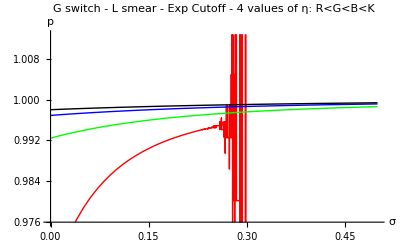

```mathematica
Plot[{pexp[σ,η[[1]]],pexp[σ,η[[2]]],pexp[σ,η[[3]]],pexp[σ,η[[4]]]},
{σ,0,.5},
AxesLabel->{σ,p},
PlotStyle->{Red,Green,Blue,Black},
PlotRange->Automatic,
PlotLabel->Style["G switch - L smear - Exp Cutoff -\n 4 values of η: R<G<B<K",FontSize->16]]
```

#### plooooooooot PSHARP

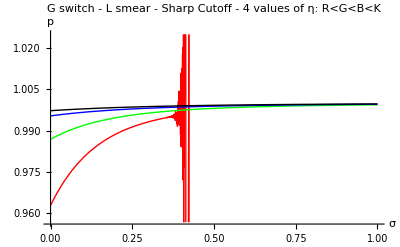

```mathematica
Plot[{psharp[σ,η[[1]]],psharp[σ,η[[2]]],psharp[σ,η[[3]]],psharp[σ,η[[4]]]},
{σ,0,1},
AxesLabel->{σ,p},
PlotStyle->{Red,Green,Blue,Black},
PlotRange->Automatic,
PlotLabel->Style["G switch - L smear - Sharp Cutoff -\n 4 values of η: R<G<B<K",FontSize->16],
PerformanceGoal->"Quality",
WorkingPrecision->48]
```

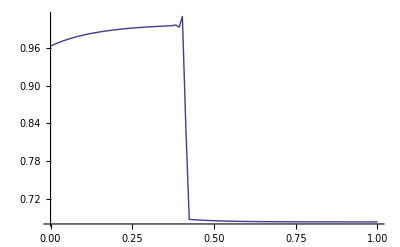
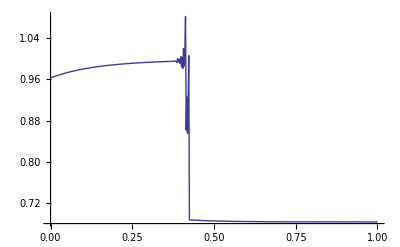
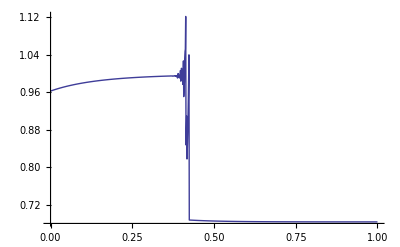

```mathematica
Table[Plot[psharp[σ,η[[1]]],{σ,0,1},PlotPoints->i,MaxRecursion->0],{i,{100,500,1000}}]
```

there’s something weird going on with sampling.

i also do not understand why there is this large flat nonzero limit as σ gets large

```mathematica
Ω:=1
α:=1
λ:=.1
ε:=0.25
```

```mathematica
Limit[pnone[σ,η],σ->∞]
```

$Aborted

```mathematica
Limit[σ/π 1/(x^2+σ^2),σ->∞]
```

0

```mathematica
Limit[psharp[σ,1],σ->∞]
```

0.

## plot p v η

#### assign the parameters numbers

```mathematica
σ:=1
Ω:=1
α:=1
λ:=.1
ε:=0.25
```

#### clear parameters of numbers when necessary

```mathematica
Clear[σ];Clear[η];Clear[Ω];Clear[α];Clear[λ];Clear[ε];
```

#### plot p v η

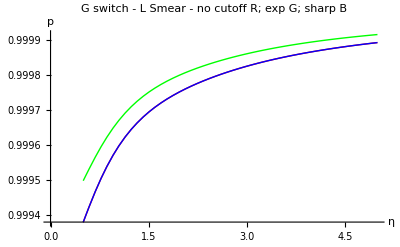

```mathematica
Plot[{pnone[σ,η],pexp[σ,η],psharp[σ,η]},{η,0.5,5},AxesLabel->{η,p},
PlotStyle->{Red,Green,Blue,Black},
PlotRange->Automatic,
PlotLabel->Style["G switch - L Smear -\n no cutoff R; exp G; sharp B",FontSize->16],
PerformanceGoal->"Quality"]
```

```mathematica
pexp[1,10]
```

2.85562×10^-29

## status

Edu suggets that the funky behaviour of the sharp cutoff (...and everything else) is “98.9% likely” to be due to issues with numerical integration of oscillatory functions

would/will address this in the future by numerically integrating using high performance values of WorkingPrecision, AccuracyGoal, & PrecisionGoal in NIntegrate